```mathematica
AutoGeneratedPackage->Automatic
```

```mathematica
<<"MultivariateStatistics`"
```

```mathematica
NormalDis[x_]:=(Erf[x/(√2)]+1)/2
```

```mathematica
NormalDis[x0_,σ_,x_]:=(Erf[((x-x0)/σ)/(√2)]+1)/2
```

```mathematica
D[(Erf[((x-x0)/σ)/(√2)]+1)/2,x]
```

(ⅇ^(-(x-x0)^2/(2 σ^2)))/(√(2 π) σ)

```mathematica
NormalDens[x0_,σ_,x_]:=(ⅇ^(-(x-x0)^2/(2 σ^2)))/(√(2 π) σ)
```

```mathematica
NormalDis[x_]:=(Erf[x/(√2)]+1)/2
```

```mathematica
NormDens[x0_,σ_,x_]:=(ⅇ^(-(x-x0)^2/(2 σ^2)))/(√(2 π) σ)
```

```mathematica
NormDens[x_]:=(ⅇ^(-(x)^2/2))/(√(2 π))
```

```mathematica
NormalDens[x_]:=(ⅇ^(-(x)^2/2))/(√(2 π))
```

```mathematica
NormDis[x_]:=(Erf[x/(√2)]+1)/2
```

```mathematica
NormaDisInv[x_]:=√2 InverseErf[0,-1+2 x]
```

```mathematica
f[x_,μ_,σ_]:=NormalDis[(Log[x]-μ)/σ]
```

```mathematica
Plot[{f[x,0,√(0.03/12)],f[x,0,√(0.3/12)]},{x,0.08,2.3},PlotRange->{0,1}]
```

⁃Graphics⁃

```mathematica
Nd[x_]:=N[(Erf[x/(√2)]+1)/2,40]
```

```mathematica
Nd[3.5]-Nd[-3.5]
```

0.999535

```mathematica
BS[s_,k_,t_,r_,d_,v_]:= s Exp[-d t]  NormalDis[(Log[(s Exp[r t-d t])/k]+(v^2 t)/2)/(v Sqrt[t])]-k Exp[-r t] NormalDis[(Log[(s Exp[r t-d t])/k]-(v^2 t)/2)/(v Sqrt[t])]
```

```mathematica
BS[s_,k_,t_,r_,v_]:= s NormalDis[(Log[(s Exp[r t])/k]+(v^2 t)/2)/(v Sqrt[t])]-k Exp[-r t] NormalDis[(Log[(s Exp[r t])/k]-(v^2 t)/2)/(v Sqrt[t])]
```

```mathematica
BS[f_,k_,t_,v_]:= f  NormalDis[(Log[f/k]+(v^2 t)/2)/(v Sqrt[t])]-k  NormalDis[(Log[f/k]-(v^2 t)/2)/(v Sqrt[t])]
```

```mathematica
BSVega[f_,k_,t_,v_]:= f  NormalDis[(Log[f/k]+(v^2 t)/2)/(v Sqrt[t])] √t
```

```mathematica
BS1[f_,k_,t_,v_]=Simplify[D[BS[f,k,t,v],f]]
```

1/2 (1+Erf[(t v^2+2 Log[f/k])/(2 √2 √t v)])

```mathematica
Simplify[D[BS1[f,k,t,v],f]]
```

(ⅇ^(-((t v^2+2 Log[f/k])^2)/(8 t v^2)))/(f √(2 π) √t v)

```mathematica
BSPut[f_,k_,v_]:=BS[f,k,v]-(f-k)
```

```mathematica
BSDigitalPut[f_,k_,v_]:=1-NormalDis[(Log[f/k]-v^2/2)/v]
```

```mathematica
BSDigitalCall[f_,k_,v_]:=NormalDis[(Log[f/k]-v^2/2)/v]
```

```mathematica
BSDigitalCall[f_,k_,v_,t_]:=NormalDis[(Log[f/k]-(v^2 t)/2)/(v Sqrt[t])]
```

```mathematica
Plot[1-BSDigitalCall[100,k,0.2,1],{k,50,150}]
```

⁃Graphics⁃

```mathematica
Essai[f_,k_,b_,v_]:=BSPut[f,k,v]-BSPut[f,b,v]-(k-b)BSDigitalPut[f,b,v]
```

```mathematica
Module[{k=150,b=142,v=0.4},Plot[Essai[f,k,b,v],{f,80,180},PlotRange->All]]
```

⁃Graphics⁃

```mathematica
Module[{k=1.50,b=1.42,v=0.4,f=1.4644},{BSPut[f,k,v],BSPut[f,b,v],BSDigitalPut[f,b,v],Essai[f,k,b,v]}]
```

{0.253175,0.207085,0.548958,0.00217415}

```mathematica
t=N[YearsBetween[{9,23,2010},{11,4,2003}]]
```

6.88493

```mathematica
NormalDis[x_]:=(Erf[x/(√2)]+1)/2
```

```mathematica
BS[f_,k_,v_]:= f  NormalDis[(Log[f/k]+v^2/2)/v]-k  NormalDis[(Log[f/k]-v^2/2)/v]
```

```mathematica
Series[BS[f,1/k,v],{k,0,1}]
```

1/2 f (1+Erf[(v^2/2+Log[f]+Log[k])/(√2 v)+O[k]^2])+(1+Erf[(-v^2/2+Log[f]+Log[k])/(√2 v)+O[k]^2]) (-1/(2 k)+O[k]^2)

```mathematica
PhiVol[m_,u_]:=Exp[m] Nd[m/u+u/2]-Nd[m/u-u/2]
```

```mathematica
PhiVol[0.47000362924574,0.05]
```

0.6

```mathematica
k-> infinity is equivalent to k* PhiVol[m,v]  with m->Log[0]
```

```mathematica
Plot3D[PhiVol[m,u],{m,-0.5,+0.5},{u,0.001,1}]
```

⁃SurfaceGraphics⁃

```mathematica
Off[FindRoot::"precw",FindRoot::"reged",FindRoot::"lstol"]
```

```mathematica
ImpVolBS[F_,K_,t_,discount_,opt_]:=Module[{o=opt/(K  discount),m=Log[F/K],ss},
ss=FindRoot[PhiVol[m,u]==o,{u,0.2,0.0001,7.},AccuracyGoal->8,WorkingPrecision->30,MaxIterations->200];ss[[1,2]]/Sqrt[t]]
```

```mathematica
ImpVolBS[F_,K_,t_,opt_]:=Module[{o=opt/K ,m=Log[F/K],ss},
ss=FindRoot[PhiVol[m,u]==o,{u,0.2,0.0001,7.},AccuracyGoal->8,WorkingPrecision->30,MaxIterations->200];ss[[1,2]]/Sqrt[t]]
```

```mathematica
ImpVolBSPut[F_,K_,t_,opt_]:=Module[{o=(opt+F-K)/K ,m=Log[F/K],ss},
ss=FindRoot[PhiVol[m,u]==o,{u,0.2,0.0001,7.},AccuracyGoal->8,WorkingPrecision->30,MaxIterations->200];ss[[1,2]]/Sqrt[t]]
```

```mathematica
ImpVolBS[F_,List[A__],t_,discount_,opt_]:=Table[ImpVolBS[F,List[A][[i]],t,discount,opt[[i]]],{i,1,Length[List[A]]}]
```

```mathematica
ImpVolBS[F_,List[A__],t_,opt_]:=Table[ImpVolBS[F,List[A][[i]],t,opt[[i]]],{i,1,Length[List[A]]}]
```

```mathematica
ImpVolBSPut[F_,List[A__],t_,opt_]:=Table[ImpVolBSPut[F,List[A][[i]],t,opt[[i]]],{i,1,Length[List[A]]}]
```

```mathematica
BS[f_,k_,t_,v_,B_]:=B( f  Nd[(Log[f/k]+(v^2 t)/2)/(v Sqrt[t])]-k  Nd[(Log[f/k]-(v^2 t)/2)/(v Sqrt[t])])
```

```mathematica
Off[FindRoot::"precw",FindRoot::"lstol"]
```

```mathematica
op=BS[160,100,1,0.07,0.42]
```

69.1317

```mathematica
ImpVolBS[160,100,1,0.43,op]
```

12.2000005468749996850874595112

```mathematica
Test de la validite de l'interpolation lineaire de la vol
```

```mathematica
Op= Interpolation[{{80,BS[100,80,2,0.2,1]},{90,BS[100,90,2,0.2,1]},{120,BS[100,120,2,0.2,1]},{150,BS[100,150,2,0.2,1]}}]
```

InterpolatingFunction[{{80.,150.}},<>]

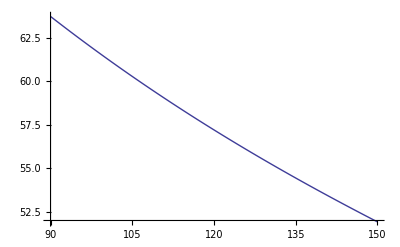

```mathematica
Plot[Op[x],{x,90,150}]
```

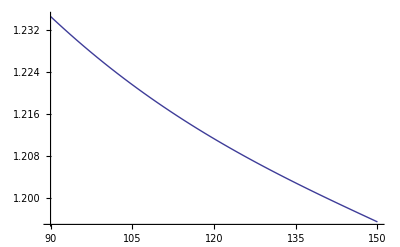

```mathematica
Plot[ImpVolBS[100,k,2,1,Op[k]],{k,90,150}]
```

```mathematica
Asymptotics Analysis
```

```mathematica
PhiVol[0.47000362924574,0.13]
```

0.600006

```mathematica
Limit[Erf[x],x->∞]
```

1

```mathematica
NormalDis[x]
```

1/2 (1+Erf[x/(√2)])

```mathematica
Positive values
```

```mathematica
Probleme Norm[x] : devrait donner 1 a l'infini
```

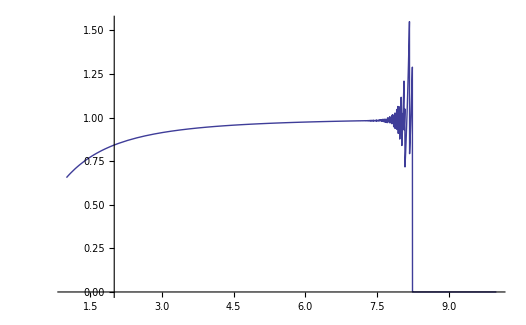

```mathematica
Plot[Apply[(Module[{x=SetPrecision[#,500]},N[#(1-NormalDis[#])/NormalDens[#],500]])&,{x}],{x,1,10}]
```

```mathematica
AsymptoticNd[x_]:=1-(ⅇ^(-x^2/2))/(√π(x/(√2)+√(x^2/2+2)))
```

```mathematica
AsymptoticN[x_]:=1-(ⅇ^(-x^2/2))/(√π((2x)/(√2)))
```

```mathematica
Solve[AsymptoticN[x]==y,x]
```

InverseFunction::ifun: Inverse functions are being used. Values may be lost for multivalued inverses. Plus…

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information. Plus…

{{x→-√ProductLog[1/(2 π (-1+y)^2)]},{x→√ProductLog[1/(2 π (-1+y)^2)]}}

```mathematica
InverseAsymptoticN[y_]:=√ProductLog[1/(2 π (-1+y)^2)]
```

```mathematica
InverseAsymptoticN2[y_]:=√ProductLog[1/(2 π (y)^2)]
```

```mathematica
ss=Series[InverseAsymptoticN2[x],{x,0,1}]
```

√(2 ⅈ π Floor[(π+2 Arg[x])/(2 π)]-Log[2 ⅈ π Floor[(π+2 Arg[x])/(2 π)]+Log[1/(2 π)]-2 (2 ⅈ π Floor[(π+Arg[x])/(2 π)]+(Log[x]+O[x]^2))]+((Log[1/(2 π)]-2 Log[x])+O[x]^2)+(Log[2 ⅈ π Floor[(π+2 Arg[x])/(2 π)]+Log[1/(2 π)]-2 (2 ⅈ π Floor[(π+Arg[x])/(2 π)]+(Log[x]+O[x]^2))]-3/2 Log[2 ⅈ π Floor[(π+2 Arg[x])/(2 π)]+Log[1/(2 π)]-2 (2 ⅈ π Floor[(π+Arg[x])/(2 π)]+(Log[x]+O[x]^2))]^2+1/3 Log[2 ⅈ π Floor[(π+2 Arg[x])/(2 π)]+Log[1/(2 π)]-2 (2 ⅈ π Floor[(π+Arg[x])/(2 π)]+(Log[x]+O[x]^2))]^3)/(2 ⅈ π Floor[(π+2 Arg[x])/(2 π)]+((Log[1/(2 π)]-2 Log[x])+O[x]^2))^3-(Log[2 ⅈ π Floor[(π+2 Arg[x])/(2 π)]+Log[1/(2 π)]-2 (2 ⅈ π Floor[(π+Arg[x])/(2 π)]+(Log[x]+O[x]^2))]-1/2 Log[2 ⅈ π Floor[(π+2 Arg[x])/(2 π)]+Log[1/(2 π)]-2 (2 ⅈ π Floor[(π+Arg[x])/(2 π)]+(Log[x]+O[x]^2))]^2)/(2 ⅈ π Floor[(π+2 Arg[x])/(2 π)]+((Log[1/(2 π)]-2 Log[x])+O[x]^2))^2+Log[2 ⅈ π Floor[(π+2 Arg[x])/(2 π)]+Log[1/(2 π)]-2 (2 ⅈ π Floor[(π+Arg[x])/(2 π)]+(Log[x]+O[x]^2))]/(2 ⅈ π Floor[(π+2 Arg[x])/(2 π)]+((Log[1/(2 π)]-2 Log[x])+O[x]^2)))

```mathematica
Simplify[ ss /. Arg[x]->0]
```

√(Log[1/(2 π)]-2 Log[x]+(-1+1/(Log[1/(2 π)]-2 Log[x])^3-1/(Log[1/(2 π)]-2 Log[x])^2+1/(Log[1/(2 π)]-2 Log[x])) Log[Log[1/(2 π)]-2 Log[x]]+((-3+Log[1/(2 π)]-2 Log[x]) Log[Log[1/(2 π)]-2 Log[x]]^2)/(2 (Log[1/(2 π)]-2 Log[x])^3)+Log[Log[1/(2 π)]-2 Log[x]]^3/(3 (Log[1/(2 π)]-2 Log[x])^3))+O[x]^2

```mathematica
Negative Values
```

```mathematica
AsymptoticNdm[x_]:=(ⅇ^(-x^2/2))/(√π(-x/(√2)+√(x^2/2+2)))
```

```mathematica
AsymptoticNd2[x_]:=If[x>0,AsymptoticNd[x],AsymptoticNdm[x]]
```

```mathematica
AsymptoticPhiVol[m_,u_]:=If[m≥0,Exp[m] AsymptoticNd[m/u+u/2]-AsymptoticNd[m/u-u/2],Exp[m] AsymptoticNdm[m/u+u/2]-AsymptoticNdm[m/u-u/2]]
```

```mathematica
Precision variable
```

```mathematica
PhiVolInitial[m_,u_]:=Exp[m] NormalDis[m/u+u/2]-NormalDis[m/u-u/2]
```

```mathematica
PhiVol[m_,u_,p_]:=If[Abs[m/u]>5,AsymptoticPhiVol2[SetPrecision[m,p],SetPrecision[u,p]],PhiVolInitial[SetPrecision[m,p],SetPrecision[u,p]]]
```

```mathematica
Using ordinary function as  -> implementation in C++
```

```mathematica
AsymptoticPhiVol2[m_,u_]:=If[m≥0,-1+ⅇ^m+2 ⅇ^(-((-2 m+u^2)^2)/(8 u^2)) √(2/π) u* (1/(2 m+u *(-u+√(16-4 m+(4 m^2)/u^2+u^2)))-1/(2 m+u *(u+√(16+4 m+(4 m^2)/u^2+u^2)))),2 ⅇ^(-((-2 m+u^2)^2)/(8 u^2)) √(2/π) u *(1/(2 m-u* (u+√(16-4 m+(4 m^2)/u^2+u^2)))-1/(2 m+u* (u-√(16+4 m+(4 m^2)/u^2+u^2))))]
```

```mathematica
Plot[PhiVol[m,1],{m,4.999,5.001}]
```

⁃Graphics⁃

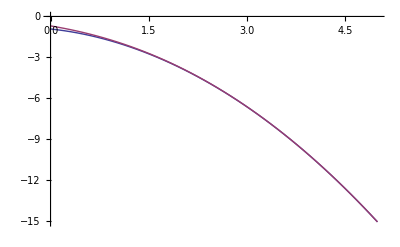

```mathematica
Plot[{Log[1-AsymptoticNd2[x]],Log[1-NormalDis[x]]},{x,0,5}]
```

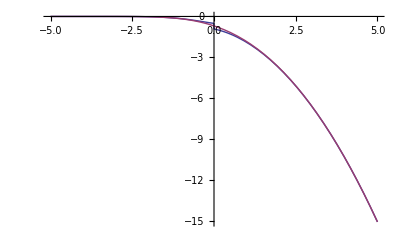

```mathematica
Plot[{Log[1-AsymptoticNd2[x]],Log[1-NormalDis[x]]},{x,-5,5}]
```

```mathematica
Simplify[Exp[m] AsymptoticNd[m/u+u/2]-AsymptoticNd[m/u-u/2]]
```

-1+ⅇ^m+2 ⅇ^(-((-2 m+u^2)^2)/(8 u^2)) √(2/π) u (1/(2 m+u (-u+√(16-4 m+(4 m^2)/u^2+u^2)))-1/(2 m+u (u+√(16+4 m+(4 m^2)/u^2+u^2))))

```mathematica
Simplify[Series[ (1/(2 m+u (-u+√(16-4 m+(4 m^2)/u^2+u^2)))-1/(2 m+u (u+√(16+4 m+(4 m^2)/u^2+u^2)))),{u,0,3}],m>0]
```

u^2/(4 m^2)+O[u]^4

```mathematica
2 ⅇ^(-((-2 m+u^2)^2)/(8 u^2)) √(2/π) u (1/(2 m-u (u+√(16-4 m+(4 m^2)/u^2+u^2)))-1/(2 m+u (u-√(16+4 m+(4 m^2)/u^2+u^2))))
```

```mathematica
Simplify[Series[ (1/(2 m-u (u+√(16-4 m+(4 m^2)/u^2+u^2)))-1/(2 m+u (u-√(16+4 m+(4 m^2)/u^2+u^2)))),{u,0,3}],m<0]
```

u^2/(4 m^2)+O[u]^4

```mathematica
2 ⅇ^(-((-2 m+u^2)^2)/(8 u^2)) √(2/π)  u^3/(4 m^2)
```

```mathematica
Expand[-((-2 m+u^2)^2)/(8 u^2)]
```

m/2-m^2/(2 u^2)-u^2/8

```mathematica
Solve[Exp[-m^2/(2 u^2)] u^3==y,u]
```

InverseFunction::ifun: Inverse functions are being used. Values may be lost for multivalued inverses. Plus…

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information. Plus…

{{u→-m/(√3 √ProductLog[m^2/(3 y^(2/3))])},{u→m/(√3 √ProductLog[m^2/(3 y^(2/3))])},{u→-m/(√3 √ProductLog[-((-1)^(1/3) m^2)/(3 y^(2/3))])},{u→m/(√3 √ProductLog[-((-1)^(1/3) m^2)/(3 y^(2/3))])},{u→-m/(√3 √ProductLog[((-1)^(2/3) m^2)/(3 y^(2/3))])},{u→m/(√3 √ProductLog[((-1)^(2/3) m^2)/(3 y^(2/3))])}}

```mathematica
Un equivalent de phivol pour m>0 est     -1+ⅇ^m+2 ⅇ^(m/2-m^2/(2 u^2)) √(2/π)u^3/(4 m^2)=-1+ⅇ^m+(2 ⅇ^(m/2))/(4 m^2) √(2/π)  h(m,u)
```

```mathematica
Un equivalent de phivol pour m<0 est          2 ⅇ^(m/2-m^2/(2 u^2)) √(2/π)  u^3/(4 m^2)=(2 ⅇ^(m/2))/(4 m^2) √(2/π)  h(m,u)
```

```mathematica
where h(m,u)=ⅇ^(-m^2/(2 u^2))u^3  and hInverse(m,y)=m/(√3 √ProductLog[m^2/(3 y^(2/3))])
```

```mathematica
En Utilisant uniquement les equivalents on a :
```

```mathematica
AsymptoticPhiVol3[m_,u_]:=If[m≥0,-1+ⅇ^m+2 ⅇ^(m/2-m^2/(2 u^2)) √(2/π)u^3/(4 m^2), 2 ⅇ^(m/2-m^2/(2 u^2)) √(2/π)  u^3/(4 m^2)]
```

```mathematica
Ce qui permet de trouver un equivalent de la formule de black and sholes
```

```mathematica
NormalDis[x_]:=1/2 (Erf[x/(√2)]+1)
```

```mathematica
BS[f_,k_,t_,v_]:= f  NormalDis[(Log[f/k]+(v^2 t)/2)/(v Sqrt[t])]-k  NormalDis[(Log[f/k]-(v^2 t)/2)/(v Sqrt[t])]
```

```mathematica
Clear[f,k,T,t,v,σ,NormalDis,BS]
```

```mathematica
Simplify[-D[BS[f,k,t,v],k]]
```

1/2 (1-Erf[(t v^2-2 Log[f/k])/(2 √2 √t v)])

```mathematica
Solve[1/2 (1-Erf[(u^2-2 Log[f/A])/(2 √2 u)])==Subscript[D, A],u]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information. More…

{{u→√2 InverseErf[0,1-2 D_A]-√2 √(InverseErf[0,1-2 D_A]^2+Log[f/A])},{u→√2 InverseErf[0,1-2 D_A]+√2 √(InverseErf[0,1-2 D_A]^2+Log[f/A])}}

```mathematica
D[1/2 (1-Erf[(u^2-2 Log[f/k])/(2 √2 u)]),k]
```

-(ⅇ^(-((u^2-2 Log[f/k])^2)/(8 u^2)))/(k √(2 π) u)

```mathematica
BS[f_,k_,t_,v_]:=Module[{m=Log[f/k],u=v Sqrt[t]},k PhiVol[m,u]]
```

```mathematica
PhiVol[m_,u_]:=Exp[m] Nd[m/u+u/2]-Nd[m/u-u/2]
```

```mathematica
AsymptoticBS[f_,k_,t_,v_]:=Module[{m=Log[f/k],u=v Sqrt[t]},k AsymptoticPhiVol3[m,u]]
```

```mathematica
Equivalent for the digital option when k->0
```

```mathematica
DigitalCall=1+√(1/(2π)) (ⅇ^(-1/2((t v^2-2 Log[f/k])/(2 √t v))^2))/((t v^2-2 Log[f/k])/(2 √t v))
```

```mathematica
Module[{t=1,v=0.2,f=1},Plot[1+√(1/(2π)) (ⅇ^(-1/2((t v^2-2 Log[f/k])/(2 √t v))^2))/((t v^2-2 Log[f/k])/(2 √t v)),{k,0,0.5},PlotRange->All]]
```

⁃Graphics⁃

```mathematica
Equivalent for the digital option when k->∞
```

```mathematica
DigitalCall=√(1/(2π)) (ⅇ^(-1/2((t v^2-2 Log[f/k])/(2 √t v))^2))/((t v^2-2 Log[f/k])/(2 √t v))
```

```mathematica
Module[{t=1,v=0.2,f=1},Plot[√(1/(2π)) (ⅇ^(-1/2((t v^2-2 Log[f/k])/(2 √t v))^2))/((t v^2-2 Log[f/k])/(2 √t v)),{k,1,5},PlotRange->All]]
```

⁃Graphics⁃

```mathematica
Solve[√(1/(2π))(ⅇ^(-u^2/2))/u==x,u]
```

InverseFunction::ifun: Inverse functions are being used. Values may be lost for multivalued inverses. More…

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information. More…

{{u→-√ProductLog[1/(2 π x^2)]},{u→√ProductLog[1/(2 π x^2)]}}

```mathematica
Subscript[D, A]=-1/2 (1-Erf[(u^2-2 Log[f/A])/(2 √2 u)]);
Subscript[d, A]=(ⅇ^(-((u^2-2 Log[f/A])^2)/(8 u^2)))/(A √(2 π) u)
```

```mathematica
<<"Splines`"
```

```mathematica
spline=SplineFit[pts,Cubic]
```

```mathematica
?SplineFit
```

SplineFit[points, type] generates a SplineFunction object of the given type from the points.  Supported types are Cubic, CompositeBezier, and Bezier. More…

```mathematica
NonParametricLogVolatilityInterpolate[strikeprobaList_,indexdebut_,indexfin_,k_]:=Module[{
A=First[strikeprobaList][[1]],VA=First[strikeprobaList][[2]],B=Last[strikeprobaList][[1]],VB=Last[strikeprobaList][[2]],interpo,},
interpo=Interpolation[strikeprobaList,InterpolationOrder->3];
If[k>B,
VB(k/B)^indexfin,
If[k<A,
VA(k/A)^indexdebut,
interpo[k]]]]
```

```mathematica
Module[{ll},ll={{1,0.1},{2,0.2},{3,0.5},{5,0.8},{6,0.9},{7,0.95}};
Plot[NonParametricLogVolatilityInterpolate[ll,-2,0.5,k],{k,0.1,10}]]
```

⁃Graphics⁃

```mathematica
pour la vol implicite :
```

```mathematica
si m>0  VolImplicit =Log[f/k]/(√(3T) √ProductLog[Log[f/k]^(2/3)/(3 ((C+k-f)^(2/3)((2π)/(f k))^(1/3)))])
```

```mathematica
si m<0  VolImplicit =Log[k/f]/(√(3T) √ProductLog[Log[k/f]^(2/3)/(3 ((C)^(2/3)((2π)/(f k))^(1/3)))])
```

```mathematica
Series[Log[f x]/(√(3T) √ProductLog[Log[f x]^(2/3)/(3 ((C+1/x-f)^(2/3)((2π x)/f)^(1/3)))]),{x,0,1}]
```

((2 π)^(1/6) (Log[f]+Log[x]))/(√T √((Log[f]+Log[x])^(2/3)/(1/f)^(1/3)) x^(1/6))+((Log[f]+Log[x])^(5/3) x^(1/6))/(6 (1/f)^(1/3) (2 π)^(1/6) √T √((Log[f]+Log[x])^(2/3)/(1/f)^(1/3)))-((Log[f]+Log[x])^(7/3) √x)/(24 ((1/f)^(2/3) √(2 π) √T √((Log[f]+Log[x])^(2/3)/(1/f)^(1/3))))+((2 π)^(1/6) (Log[f]+Log[x]) (C-f-(13 f (Log[f]+Log[x])^2)/(288 π)) x^(5/6))/(3 √T √((Log[f]+Log[x])^(2/3)/(1/f)^(1/3)))+(π^(1/6) (Log[f]+Log[x]) (-(4 2^(2/3) (C-f) (Log[f]+Log[x])^(2/3))/(9 (1/f)^(1/3) π^(1/3))+(5 (C-f) (Log[f]+Log[x])^(2/3))/(18 (1/f)^(1/3) (2 π)^(1/3))+(Log[f]+Log[x])^(8/3)/(96 2^(1/3) (1/f)^(4/3) π^(4/3))+(7 (Log[f]+Log[x])^(2/3) (C-f-(13 f (Log[f]+Log[x])^2)/(288 π)))/(18 (1/f)^(1/3) (2 π)^(1/3))) x^(7/6))/(2 2^(5/6) √T √((Log[f]+Log[x])^(2/3)/(1/f)^(1/3)))+O[x]^(3/2)

```mathematica
Series[Log[k/f]/(√(3T) √ProductLog[Log[k/f]^(2/3)/(3 ((C)^(2/3)((2π)/(f k))^(1/3)))]),{k,0,1}]
```

((2 π)^(1/6) (Log[1/f]+Log[k]))/(√T √((Log[1/f]+Log[k])^(2/3)/(C^(2/3) (1/f)^(1/3))) k^(1/6))+((Log[1/f]+Log[k])^(5/3) k^(1/6))/(6 C^(2/3) (1/f)^(1/3) (2 π)^(1/6) √T √((Log[1/f]+Log[k])^(2/3)/(C^(2/3) (1/f)^(1/3))))-((Log[1/f]+Log[k])^(7/3) √k)/(24 (C^(4/3) (1/f)^(2/3) √(2 π) √T √((Log[1/f]+Log[k])^(2/3)/(C^(2/3) (1/f)^(1/3)))))-(13 (f (Log[1/f]+Log[k])^3) k^(5/6))/(432 (C^2 (2 π)^(5/6) √T √((Log[1/f]+Log[k])^(2/3)/(C^(2/3) (1/f)^(1/3)))))-(37 (Log[1/f]+Log[k])^(11/3) k^(7/6))/(20736 (2^(1/6) C^(8/3) (1/f)^(4/3) π^(7/6) √T √((Log[1/f]+Log[k])^(2/3)/(C^(2/3) (1/f)^(1/3)))))+O[k]^(3/2)

```mathematica
on a donc en k->+∞  une queue en  α (Log[k])^(2/3)k^(1/6)   et en 0 une queue en α (Log[k])^(2/3)/k^(1/6)
```

```mathematica
AsymptoticBS[f_,k_,T_,σ_]:=If[f>k,(f-k)+k (√(f/(2π k)) ⅇ^(-Log[f/k]^2/(2 σ^2 T)) (σ^3 T^(3/2))/Log[f/k]^2),k (2 √(f/(2π k)) ⅇ^(-Log[f/k]^2/(2 σ^2 T)) (σ^3 T^(3/2))/Log[f/k]^2)]
```

```mathematica
AsymptoticBSTimeValue[f_,k_,T_,σ_]:=k (√(f/(2π k)) ⅇ^(-Log[f/k]^2/(2 σ^2 T)) (σ^3 T^(3/2))/Log[f/k]^2)
```

```mathematica
AsymptoticBSVolImplicit[f_,k_,T_,C_]:=If[f>k,Log[f/k]/(√(3T) √ProductLog[Log[f/k]^(2/3)/(3 ((C+k-f)^(2/3)((2π)/(f k))^(1/3)))]),Log[k/f]/(√(3T) √ProductLog[Log[k/f]^(2/3)/(3 ((C)^(2/3)((2π)/(f k))^(1/3)))])]
```

```mathematica
AsymptoticBSVolImplicit[120.67187829978027,123.28752916049203,1,0.094364994808302072]
```

0.0141298

```mathematica
ImpVolBS[120.67187829978027,123.28752916049203,1,0.094364994808302072]
```

0.0166268989641901595645977215595

```mathematica
Plot[{AsymptoticBSVolImplicit[120.67187829978027,123.28752916049203,1,10^(-x)],ImpVolBS[120.67187829978027,123.28752916049203,1,10^(-x)]},{x,1,50},PlotRange->All]
```

⁃Graphics⁃

```mathematica
AsymptoticBSVolImplicit[120.67187829978027,123.28752916049203,1,0.0000094364994808302072]
```

0.0055211

```mathematica
ImpVolBS[120.67187829978027,123.28752916049203,1,0.0000094364994808302072]
```

0.00557313420457652250187980906696

```mathematica
AsymptoticBSTimeValue[137,100,1,0.0025]
```

3.79104960260944×10^-3449

```mathematica
xx1=AsymptoticBS[137,100,1,0.025]
```

37.

```mathematica
SetPrecision[xx1-37,30]
```

1.42108547152020037174224853516×10^-14

```mathematica
AsymptoticBSVolImplicit[137,100,1,xx1]
```

Power::infy: Infinite expression 1/0. encountered. More…

0

```mathematica
xx1=BS[137,100,1,0.025]
```

37.

```mathematica
ImpVolBS[137,100,1,1,xx1]
```

FindRoot::reged: The point {0.000100000000000000004792173602386} is at the edge of the search region {0.000100000000000000004792173602386, 15.} in coordinate 1 and the computed search direction points outside the region. More…

0.000100000000000000004792173602386

```mathematica
AsymptoticPhiVolInverse[m_,y_]:=Module[{x},If[m≥0,x=((y+1-ⅇ^m)/((2 ⅇ^(m/2))/(4 m^2) √(2/π)));m/(√3 √ProductLog[m^2/(3 x^(2/3))]),
x=y/((2 ⅇ^(m/2))/(4 m^2) √(2/π));m/(√3 √ProductLog[m^2/(3 x^(2/3))])]]
```

```mathematica
xx=AsymptoticPhiVol2[1.6,0.07]
```

3.95303

```mathematica
h[m_,u_]:=(2 ⅇ^(m/2))/(4 m^2) √(2/π)ⅇ^(-m^2/(2 u^2))u^3
```

```mathematica
hInverse[m_,y_]:=m/(√3 √ProductLog[m^2/(3 (y/((2 ⅇ^(m/2))/(4 m^2) √(2/π)))^(2/3))])
```

```mathematica
xx1=h[1.6,0.2]
```

3.51376×10^-17

```mathematica
hInverse[1.6,xx1]
```

0.2

```mathematica
AsymptoticPhiVolSumToDo[m_,u_]:={-1+ⅇ^m,2 ⅇ^(m/2-m^2/(2 u^2)) √(2/π)u^3/(4 m^2)}
```

```mathematica
xx=AsymptoticPhiVolSumToDo[1.1,0.2]
```

{2.00417,1.23416×10^-9}

```mathematica
Dans certain cas 119 chiffre de precision sont necessaire
```

```mathematica
m=Log[1.6];u=0.07;p=20;
xx=AsymptoticPhiVol[SetPrecision[m,p],SetPrecision[u,p]];
AsymptoticPhiVolInverse[SetPrecision[m,p],xx]
```

0.0699062

```mathematica
Plot3D[PhiVol[m,u],{m,-0.5,+0.5},{u,0.01,1}]
```

-Graphics3D-

```mathematica
LogNormal Distribution
```

```mathematica
LogNormalDens[x0_,σ0_,x_]:=If[x≤0,0,Exp[-1/2(Log[x/x0]/σ0)^2]/(x σ0 √(2π))]
```

```mathematica
LogNormalDistrib[x0_,σ0_,x_]:=If[x≤0,0,(1-Erf[(-Log[x/x0])/(√2 σ0)])/2]
```

```mathematica
LogNormalQuantile[x0_,σ0_,y_]:=ⅇ^(-√2 σ0 InverseErf[0,1-2 y]) x0
```

```mathematica
pd=LogNormalDistribution[x0,σ0];
CDF[pd,x]
```

1/2 (1+Erf[(-x0+Log[x])/(√2 σ0)])

```mathematica
Black and Scholes formula with a controled precision
```

```mathematica
BSp[f_,k_,t_,v_,bond_,p_]:= Module[{m=SetPrecision[f,p]/SetPrecision[k,p],V=SetPrecision[v,p] √SetPrecision[t,p]},(SetPrecision[f,p] NormalDis[(Log[m]+V^2/2)/V]-SetPrecision[k,p]  NormalDis[(Log[m]-V^2/2)/V])SetPrecision[bond,p]]
```

```mathematica
BSp[1.6393062059132,1.,1.,0.07,0.43859007915026,30]
```

0.28039335945272721951680516704

```mathematica
BSp[1.6393062059132,1.,1.,0.08,0.43859007915026,30]
```

0.28039335945496535654560672719

```mathematica
BS[1.6393062059132,1.,1.,0.07,0.43859007915026]
```

0.280393

```mathematica
lglist=LegendreCoeffs[30,-1,1];
```

```mathematica
Module[{S=100,T=10,V=0.04,κ=0.09,θ=0.05,ϵ=0.2,ρ=-0.5},tt=Table[{K,ImpVolBS[S,K,T,1,SVCall[S,K,V,T,κ,θ,ϵ,ρ]]},{K,10,1000,2}];ListPlot[tt,Joined->True,PlotRange->All]]
```

⁃Graphics⁃

```mathematica
Merton Formula
```

```mathematica
MertonCall[F_,K_,t_,σ_,λ_,muJ_,σJ_,Nbterms_]:=Module[
{λp,i,r},
λp=λ Exp[muJ+σJ^2/2];
Sum[
r=Exp[i Log[λ t]]/Gamma[i+1];
r  BS[F Exp[(λ -λp)t +i (muJ+(σJ^2 )/2)],K,t,Sqrt[σ^2+i σJ^2/t]],{i,0,Nbterms}] ⅇ^(-λ t)]
```

```mathematica
Module[{S=100,K=100,T=1,sig=0.2,λ=0.01,μJ=0.0,sigJ=0.2,nbterms=100},
MertonCall[S,K,T,sig,λ,μJ,sigJ,nbterms]]
```

7.99895

```mathematica
Module[{S=100,K=100,T=7,sig=0.2,λ=0.01,μJ=0.0,sigJ=0.2,nbterms=100},
MertonCall[S,K,T,sig,λ,μJ,sigJ,nbterms]]
```

20.9663

```mathematica
MertonPut[F_,K_,t_,σ_,λ_,muJ_,σJ_,Nbterms_]:=Module[
{λp,i,r},
λp=λ Exp[muJ+σJ^2/2];
Sum[
r=Exp[i Log[λ t]]/Gamma[i+1];
r  (BS[F Exp[(λ -λp)t +i (muJ+(σJ^2 )/2)],K,t,Sqrt[σ^2+i σJ^2/t]]-(F-K)),{i,0,Nbterms}] ⅇ^(-λ t)]
```

```mathematica
Module[{S=100,K=110,T=7,sig=0.2,λ=0.01,μJ=0.0,sigJ=0.2,nbterms=100},
{MertonCall[S,K,T,sig,λ,μJ,sigJ,nbterms],MertonPut[S,K,T,sig,λ,μJ,sigJ,nbterms]}]
```

{17.3595,27.3595}

```mathematica
Formule utilisant le pourcentage de vol en jump
```

```mathematica
MertonCallPercentJ[F_,K_,t_,σT_,λ_,μJ_,pJ_,Nbterms_]:=Module[
{λp,i,σ,σp},
σ=√(1-pJ)σT;
σJ=√(pJ/λ)σT;
λp=ⅇ^(μJ+σJ^2/2) λ;
Sum[(t λ)^i/Gamma[1+i]  BS[ⅇ^(t (λ-λp)+i (μJ+σJ^2/2)) F,K,t,√(σ^2+(i σJ^2)/t)],{i,0,Nbterms}] ⅇ^(-λ t)]
```

```mathematica
Module[{S=100,K=370,T=7,sigtotal=0.25,λ=1,μJ=0.0,pJ=0.95,nbterms=100,F,r=0.08},
F=S Exp[r T ];
{MertonCallPercentJ[F,K,T,sigtotal,λ,μJ,pJ,nbterms]}]
```

{11.8448}

```mathematica
Module[{S=100,K=110,T=7,sigtotal=0.2,λ=0.01,μJ=0.0,pJ=0.09,nbterms=100},
{MertonCallPercentJ[S,K,T,sigtotal,λ,μJ,pJ,nbterms]}]
```

{17.2155}

```mathematica
Module[{S=100,K=110,T=7,sigtotal=0.25,λ=0.01,μJ=0.0,pJ=0.8,nbterms=100},
{MertonCallPercentJ[S,K,T,sigtotal,λ,μJ,pJ,nbterms]}]
```

{25.2961}

```mathematica
Clear[σJ]
```

```mathematica
Sqrt[σ^2+i σJ^2/t]
```

√(σ^2+(i σJ^2)/t)

```mathematica
F Exp[(λ -λp)t +i (muJ+(σJ^2 )/2)]
```

ⅇ^(t (λ-λp)+i (muJ+σJ^2/2)) F

```mathematica
Exp[i Log[λ t]]/Gamma[i+1]
```

(t λ)^i/Gamma[1+i]

```mathematica
λ Exp[muJ+σJ^2/2]
```

ⅇ^(muJ+σJ^2/2) λ

```mathematica
Approximation of N[x]
```

```mathematica
Erf1[x_]:=Module[{a1=0.0705230784,a2=0.0422820123,a3=0.0092705272,a4=0.001520143,a5=0.0002765672,a6=0.000430638},1-1/((1+a1 x+a2 x^2+a3 x^3+a4 x^4+a5 x^5+a6 x^6)^16)]
```

```mathematica
Erf2[x_]:=If[x>0,Erf1[x],-Erf1[-x]]
```

```mathematica
Erf3[x_]:=2/(√π)(x-x^3/3+x^5/(5 2!)-x^7/(7 3!)+x^9/(9 4!)-x^11/(11 5!)+x^13/(13 6!)-x^15/(15 7!)+x^17/(17 8!)-x^19/(19 9!)+x^21/(21 10!)-x^23/(23 11!)+x^25/(25 12!)-x^27/(27 13!)+x^29/(29 14!)-x^31/(31 15!)+x^33/(33 16!)-x^35/(35 17!))
```

```mathematica
Erf4[x_,n_]:=2/(√π)(x-x^3/3+Sum[(-1)^i x^(2i+1)/((2i+1)i!),{i,2,n}])
```

```mathematica
ErfDefinitif[x_]:=If[Abs[x]<4,Erf4[x,62],Erf2[x]]
```

```mathematica
Plot[Erf[x]-Erf4[x,52],{x,-6.1,+6.1},PlotRange->{-10^-5,10^-5}]
```

⁃Graphics⁃

```mathematica
Plot[Erf[x]-Erf2[x],{x,-6.1,+6.1},PlotRange->{-2 10^-6,2 10^-6}]
```

⁃Graphics⁃

```mathematica
Plot[N[Erf[SetPrecision[x,30]],30]-ErfDefinitif[x],{x,-6.1,+6.1},PlotRange->{-2 10^-8,2 10^-8}]
```

⁃Graphics⁃

```mathematica
Plot[Log[Abs[1-ErfDefinitif[x]]]/Log[10],{x,0,7}]
```

Plot::plnr: Log[Abs[1 - ErfDefinitif[x]]]/Log[10] is not a machine-size real number at x = 4.93998. Plus…

Plot::plnr: Log[Abs[1 - ErfDefinitif[x]]]/Log[10] is not a machine-size real number at x = 4.87363. Plus…

Plot::plnr: Log[Abs[1 - ErfDefinitif[x]]]/Log[10] is not a machine-size real number at x = 4.83714. Plus…

General::stop: Further output of Plot :: "plnr" will be suppressed during this calculation. Plus…

⁃Graphics⁃

```mathematica
Bivariate
```

```mathematica
BivariateDensity[x_,y_,ρ_]:=(ⅇ^((-x^2-y^2+2 x y ρ)/(2 (1-ρ^2))))/(2 π √(1- ρ^2))
```

```mathematica
BivariateDensity[x0_,σ0_,x1_,σ1_,ρ_,x_,y_]:=BivariateDensity[(x-x0)/σ0,(y-x1)/σ1,ρ]
```

```mathematica
BivariateCummulative2D[x_,Y_,ρ_]:=Module[{y},NIntegrate[ (ⅇ^(-y^2/2)  (1+ Erf[(x-y ρ)/(√2 √(1-ρ^2))]))/(2 √(2π)),{y,-Infinity ,Y}]]
```

```mathematica
BivariateCummulative2D[S1_,σ1_,S2_,σ2_,ρ_,x_,Y_]:=Module[{y},NIntegrate[ (ⅇ^(-y^2/2)  (1+ Erf[(((x-S1)/σ1)-y ρ)/(√2 √(1-ρ^2))]))/(2 √(2π)),{y,-Infinity ,((Y-S2)/σ2)}]]
```

```mathematica
DyBivariateCummulative2D[x_,y_,ρ_]:= (ⅇ^(-y^2/2)  (1+ Erf[(x-y ρ)/(√2 √(1-ρ^2))]))/(2 √(2π))
```

```mathematica
DyBivariateCummulative2D[S1_,σ1_,S2_,σ2_,ρ_,K1_,K2_]:= 1/σ2 DyBivariateCummulative2D[(K1-S1)/σ1,(K2-S2)/σ2,ρ]
```

```mathematica
DxBivariateCummulative2D[x_,y_,ρ_]:=DyBivariateCummulative2D[y,x,ρ]
```

```mathematica
DxBivariateCummulative2D[S1_,σ1_,S2_,σ2_,ρ_,K1_,K2_]:= 1/σ1 DxBivariateCummulative2D[(K1-S1)/σ1,(K2-S2)/σ2,ρ]
```

```mathematica
BivariateCummulative2D[x_,Y_,ρ_]:=Module[{y},NIntegrate[ (ⅇ^(-y^2/2)  NormalDis[(x-y ρ)/(√(1-ρ^2))])/(√(2π)),{y,-Infinity ,Y}]]
```

```mathematica
BivariateCummulative2D[x_,Y_,ρ_]:=Module[{y},NIntegrate[ (ⅇ^(-y^2/2)  NormalDis[(x-y ρ)/(√(1-ρ^2))])/(√(2π)),{y,-Infinity ,Y}]]
```

```mathematica
BivariateCummulative2D[1,1,0.5]
```

0.745204

```mathematica
Test Bivariate Karim
```

```mathematica
Module[{fxXmin =-0.61459279001802,
fxXmax=-0.040667216627551,
irXmin=-0.53157027438957,
irXmax=-0.050302698288909,
rho= 0.10000000000000,ρ},
ρ=rho;
{{BivariateCummulative2D[fxXmin,irXmin,rho],
BivariateCummulative2D[fxXmax,irXmin,rho],
BivariateCummulative2D[fxXmin,irXmax,rho],
BivariateCummulative2D[fxXmax,irXmax,rho]},
BivariateCummulative2D[fxXmin,irXmin,rho]-
BivariateCummulative2D[fxXmax,irXmin,rho]-
BivariateCummulative2D[fxXmin,irXmax,rho]+
BivariateCummulative2D[fxXmax,irXmax,rho],
NIntegrate[(ⅇ^((-x^2-y^2+2 x y ρ)/(2 (1-ρ^2))))/(2 π √(1- ρ^2)),{x,fxXmin,fxXmax},{y,irXmin,irXmax}]}
]
```

{{0.0917901,0.157769,0.142496,0.248096},0.0396217,0.0396217}

```mathematica
BiLog Distribution
```

```mathematica
BiLogCummulative2D[x1_,σ1_,x2_,σ2_,ρ_,X1_,X2_]:=If[(X1≤0)||(X2≤0),0,BivariateCummulative2D[Log[X1/x1]/σ1,Log[X2/x2]/σ2,ρ]]
```

```mathematica
DyBiLogCummulative2D[x1_,σ1_,x2_,σ2_,ρ_,X1_,X2_]:=If[(X1≤0)||(X2≤0),0,DyBivariateCummulative2D[Log[X1/x1]/σ1,Log[X2/x2]/σ2,ρ]/(σ2 X2)]
```

```mathematica
Module[{
F1=0.0418,
α1=0.2,
F2=0.0418,
α2=0.25,
ρs=0.8,
},
K1=0.035;K2=0.045;
{DyBivariateCopula[LogNormalDistrib[F1,α1,K1],LogNormalDistrib[F2,α2,K2],ρs]LogNormalDens[F2,α2,K2],DyBiLogCummulative2D[F1,α1,F2,α2,ρs,K1,K2]}]
```

{1.03669,1.03669}

```mathematica
SKLAR Formula
```

```mathematica
Module[{
F1=0.0418,
α1=0.2,
F2=0.0418,
α2=0.25,
K=0.001,
T=5,
ρs=0.8,
nbSample=8000,
lglst,printflag=0
},
K1=0.035;K2=0.045;shift=0.0001;
{BivariateCopula[LogNormalDistrib[F1,α1,K1],LogNormalDistrib[F2,α2,K2],ρs],BiLogCummulative2D[F1,α1,F2,α2,ρs,K1,K2]}]
```

{0.184349,0.184349}

```mathematica
Module[{
F1=0.5,
α1=2.1,
F2=-0.01,
α2=1.8,
ρs=0.8
},
K1=0.035;K2=0.045;shift=0.0001;
{BivariateCopula[NormalDis[F1,α1,K1],NormalDis[F2,α2,K2],ρs],BivariateCummulative2D[(K1-F1)/α1,(K2-F2)/α2,ρs]}]
```

{0.352919,0.352919}

```mathematica
Integral of X *BivariateDensity  and  Y *BivariateDensity
```

```mathematica
BivariateCummulative2DY[x_,Y_,ρ_]:=Module[{y},NIntegrate[ (y ⅇ^(-y^2/2)  NormalDis[(x-y ρ)/(√(1-ρ^2))])/(√(2π)),{y,-Infinity ,Y}]]
```

```mathematica
BivariateCummulative2DX[X_,y_,ρ_]:=Module[{x},NIntegrate[ (x ⅇ^(-x^2/2) NormalDis[(y-x ρ)/(√(1-ρ^2))])/(√(2π)),{x,-Infinity ,X}]]
```

```mathematica
BivariateCummulative2DY[1,-1,0.5]
```

-0.236934

```mathematica
NIntegrate[y BivariateDensity[x,y,-0.5],{x,-Infinity,-1},{y,-Infinity,1}]
```

0.0186857

```mathematica
BivariateCummulative2DX[-1,1,-0.5]
```

-0.139671

```mathematica
NIntegrate[x BivariateDensity[x,y,-0.5],{x,-Infinity,-1},{y,-Infinity,1}]
```

-0.139671

```mathematica
Integral of X^n Y^p*BivariateDensity(X,Y)
```

```mathematica
BivariateCummulative2DYY[x_,Y_,ρ_]:=Module[{y},NIntegrate[ (y^2 ⅇ^(-y^2/2)  NormalDis[(x-y ρ)/(√(1-ρ^2))])/(√(2π)),{y,-Infinity ,Y}]]
```

```mathematica
BivariateCummulative2DXX[X_,y_,ρ_]:=Module[{x},NIntegrate[ (x^2 ⅇ^(-x^2/2) NormalDis[(y-x ρ)/(√(1-ρ^2))])/(√(2π)),{x,-Infinity ,X}]]
```

```mathematica
Integrate[(ⅇ^(-(x^2+y^2-2ρ x y)/(2(1-ρ^2))))/(2π √(1-ρ^2))(x-ρ y) y ,{x,-Infinity ,X}]
```

1/(2 π √(1-ρ^2))(y If[Re[ρ^2]<1,ⅇ^((X^2+y^2-2 X y ρ)/(2 (-1+ρ^2))) (-1+ρ^2),Integrate[ⅇ^((x^2+y^2-2 x y ρ)/(2 (-1+ρ^2))) (x-y ρ),{x,-∞,X},Assumptions→Re[ρ^2]≥1]])

```mathematica
-(y ⅇ^((X^2+y^2-2 X y ρ)/(2 (-1+ρ^2))) √(1-ρ^2))/(2 π)
```

```mathematica
Integrate[-(y ⅇ^((X^2+y^2-2 X y ρ)/(2 (-1+ρ^2))) √(1-ρ^2))/(2 π),{y,-Infinity ,Y}]
```

-1/(2 π)(√(1-ρ^2) If[Re[ρ^2]<1&&Re[(X ρ)/(-1+ρ^2)]<0,1/(2 √(-(X^2 ρ^2)/(-1+ρ^2)) √(-(Y-X ρ)^2/(-1+ρ^2)))(ⅇ^(-X^2/2) (√(2 π) X^2 ρ^2 √(-(Y-X ρ)^2/(-1+ρ^2)) Erf[√((X^2 ρ^2)/(2-2 ρ^2))]+√(-(X^2 ρ^2)/(-1+ρ^2)) (√(-(Y-X ρ)^2/(-1+ρ^2)) (√(2 π) X ρ √(1-ρ^2)+2 ⅇ^((Y-X ρ)^2/(2 (-1+ρ^2))) (-1+ρ^2))-√(2 π) X ρ √(1-ρ^2) √(-(Y-X ρ)^2/(-1+ρ^2)) Erf[(X ρ)/(√(2-2 ρ^2))]+√(2 π) X ρ (Y-X ρ) Erf[(√(-(Y-X ρ)^2/(-1+ρ^2)))/(√2)]))),Integrate[ⅇ^((X^2+y^2-2 X y ρ)/(2 (-1+ρ^2))) y,{y,-∞,Y},Assumptions→(Re[ρ^2]<1&&Re[(X ρ)/(-1+ρ^2)]≥0)||Re[ρ^2]≥1]])

```mathematica
(* apres simplification *)
```

```mathematica
BivariateCummulative2DXY[x_,y_,ρ_]:=(ⅇ^(-x^2/2) (1-ρ^2))/(√(2 π)) ( NormalDens[(y-x ρ)/(√(1- ρ^2))] √(1-ρ^2)- x ρ  NormalDis[(y-x ρ)/(√(1- ρ^2))])+ρ BivariateCummulative2DYY[x,y,ρ]
```

```mathematica
BivariateCummulative2DXYapp[X_,Y_,ρ_]:=NIntegrate[(x -ρ y)y  BivariateDensity[x,y,ρ],{x,-Infinity,X},{y,-Infinity,Y}]+ρ BivariateCummulative2DYY[X,Y,ρ]
```

```mathematica
NIntegrate[x y BivariateDensity[x,y,-0.5],{x,-Infinity,-1},{y,-Infinity,1}]
```

-0.0300907

```mathematica
{BivariateCummulative2DXY[1,0.5,-0.7],BivariateCummulative2DXYapp[1,0.5,-0.7]}
```

{-0.0772789,-0.0772789}

```mathematica
NIntegrate[y y BivariateDensity[x,y,-0.5],{x,-Infinity,-1},{y,-Infinity,1}]
```

0.0360014

```mathematica
BivariateCummulative2DYY[-1,1,-0.5]
```

0.0360014

```mathematica
Gaussian copula in 2 dimensions
```

```mathematica
DxBivariateCummulative2D[x_,y_,ρ_]:=(ⅇ^(-x^2/2) NormalDis[(y-x ρ)/(√(1-ρ^2))])/(√(2π))
```

```mathematica
DyBivariateCummulative2D[x_,y_,ρ_]:=(ⅇ^(-y^2/2) NormalDis[(x-y ρ)/(√(1-ρ^2))])/(√(2π))
```

```mathematica
BivariateCopula[x_,y_,ρ_]:=BivariateCummulative2D[NormaDisInv[x],NormaDisInv[y],ρ]
```

```mathematica
DxBivariateCopula[x_,y_,ρ_]:=If[x<0.00001,0,DxBivariateCummulative2D[NormaDisInv[x],NormaDisInv[y],ρ]/NormalDens[NormaDisInv[x]]]
```

```mathematica
DyBivariateCopula[x_,y_,ρ_]:=If[y<0.00001,0,DyBivariateCummulative2D[NormaDisInv[x],NormaDisInv[y],ρ]/NormalDens[NormaDisInv[y]]]
```

```mathematica
DxyBivariateCopula[x_,y_,ρ_]:=BivariateDensity[NormaDisInv[x],NormaDisInv[y],ρ]/(NormalDens[NormaDisInv[x]]NormalDens[NormaDisInv[y]])
```

```mathematica
(r = {{1, ρ}, {ρ, 1}};
ndist = MultinormalDistribution[{0, 0}, r])
```

MultinormalDistribution[{0,0},{{1,ρ},{ρ,1}}]

```mathematica
Simplify[PDF[ndist,{x,y}]]
```

(ⅇ^((x^2+y^2-2 x y ρ)/(2 (-1+ρ^2))))/(2 π √(1-ρ^2))

```mathematica
Integrate[(ⅇ^((x^2+y^2-2 x y ρ)/(2 (-1+ρ^2))))/(2 π √(1-ρ^2)),{x,-Infinity,X}]
```

1/(2 π √(1-ρ^2))If[Re[ρ^2]<1,ⅇ^(-y^2/2) √(π/2) (√(1-ρ^2)+√(-1+ρ^2) Erfi[(X-y ρ)/(√2 √(-1+ρ^2))]),Integrate[ⅇ^((x^2+y^2-2 x y ρ)/(2 (-1+ρ^2))),{x,-∞,X},Assumptions→Re[ρ^2]≥1]]

```mathematica
(ⅇ^(-y^2/2) √(π/2) (√(1-ρ^2)+√(-1+ρ^2) Erfi[(X-y ρ)/(√2 √(-1+ρ^2))]))/(2 π √(1-ρ^2))
```

```mathematica
Simplify[Erfi[-ⅈ x],x>0]
```

-ⅈ Erf[x]

```mathematica
(ⅇ^(-y^2/2) √(-1+ρ^2) Erfi[(-x+y ρ)/(√2 √(-1+ρ^2))])/(2 √(2 π) √(1-ρ^2))==(ⅇ^(-y^2/2) √(1-ρ^2) Erf[(-x+y ρ)/(√2 √(1-ρ^2))])/(2 √(2 π) √(1-ρ^2))
```

```mathematica
Integrate[(ⅇ^(-y^2/2) √(1-ρ^2) Erf[(-x+y ρ)/(√2 √(1-ρ^2))])/(2 √(2 π) √(1-ρ^2)),y]
```

(∫ⅇ^(-y^2/2) Erf[(-x+y ρ)/(√2 √(1-ρ^2))]ⅆy)/(2 √(2 π))

```mathematica
Integrand[x_,y_,ρ_]:=(ⅇ^(-y^2/2)  (1+ Erf[(x-y ρ)/(√2 √(1-ρ^2))]))/(2 √(2π))
```

```mathematica
Plot[ Integrand[x,2.5,0.9],{x,-5,5},PlotRange->All]
```

⁃Graphics⁃

```mathematica
Plot[ Integrand[0.5,y,0.5],{y,-5,5},PlotRange->All]
```

⁃Graphics⁃

```mathematica
Simplify[(ⅇ^(-y^2/2) √(1-ρ^2) Erf[(-x+y ρ)/(√2 √(1-ρ^2))])/(2 √(2 π) √(1-ρ^2))-(ⅇ^(-y^2/2) √(1-ρ^2) Erf[(y ρ)/(√2 √(1-ρ^2))])/(2 √(2 π) √(1-ρ^2))]
```

(ⅇ^(-y^2/2) (-Erf[(y ρ)/(√(2-2 ρ^2))]+Erf[(-x+y ρ)/(√(2-2 ρ^2))]))/(2 √(2 π))

```mathematica
D[Integrate[ (ⅇ^(-y^2/2)  (1+ Erf[(x-y ρ)/(√2 √(1-ρ^2))]))/(2 √(2π)),{y,-Infinity ,Y}],x]
```

1/(2 π √(1-ρ^2))If[Re[ρ^2]<1,ⅇ^(-x^2/2) √(π/2) (√(1-ρ^2)+√(-1+ρ^2) Erfi[(Y-x ρ)/(√2 √(-1+ρ^2))]),Integrate[ⅇ^((x^2+y^2-2 x y ρ)/(2 (-1+ρ^2))),{y,-∞,Y},Assumptions→Re[ρ^2]≥1]]

```mathematica
(ⅇ^(-x^2/2) √(π/2) (√(1-ρ^2)+√(-1+ρ^2) Erfi[(Y-x ρ)/(√2 √(-1+ρ^2))]))/(2 π √(1-ρ^2))==(ⅇ^(-x^2/2) √(π/2) (1+ Erf[(Y-x ρ)/(√2 √(1-ρ^2))]))/(2 π)==(ⅇ^(-x^2/2) NormalDis[(y-x ρ)/(√(1-ρ^2))])/(√(2π))=
```

```mathematica
CoeffBasedIntegrate[f,ModifiedHermiteCoeffs[n]]
```

```mathematica
ccn=BetweenNormalCoeffs[ccs,0,5,6]
```

```mathematica
BivariateCummulative2DApprox[x_,Y_,ρ_,legendreCoefs_]:=Module[{ccc=BetweenNormalCoeffs[legendreCoefs,-6,Y,4]},CoeffBasedIntegrate[( (1+ Erf[(x-# ρ)/(√2 √(1-ρ^2))])/2)&,ccc]];
```

```mathematica
BivariateCummulative2D[-0.1,5,0.5]
```

0.460172

```mathematica
ccs=LegendreCoeffs[10];
```

```mathematica
BivariateCummulative2DApprox[-0.1,5,0.5,ccs]
```

0.460172

```mathematica
NormalDis[x_]:=(Erf[x/(√2)]+1)/2
```

```mathematica
Simplify[Integrate[(ⅇ^(-y^2/2)  NormalDis[(x-y ρ)/(√(1-ρ^2))])/(√(2π)),{y,-3,Y}]]
```

$Aborted

```mathematica
Plot3D[BivariateCummulative2D[x,y,0.99],{x,-3,+3},{y,-3,+3}]
```

-Graphics3D-

```mathematica
Plot3D[BivariateCummulative2D[x,y,0.5],{x,-3,+3},{y,-3,+3}]
```

-Graphics3D-

```mathematica
BivariateCopula[1,0.1,0.1]
```

0.0999997

```mathematica
Plot3D[BivariateCopula[x,y,0.],{x,0.01,0.99},{y,0.01,0.99}]
```

⁃SurfaceGraphics⁃

```mathematica
Plot3D[BivariateCopula[x,y,0.99],{x,0.01,0.99},{y,0.01,0.99}]
```

⁃SurfaceGraphics⁃

```mathematica
Plot3D[BivariateCopula[x,y,-0.99],{x,0.01,0.99},{y,0.01,0.99}]
```

⁃SurfaceGraphics⁃

```mathematica
Normal Call and Normal Volatility
```

```mathematica
NormalCall[F_,σ_,K_,T_]:=(F-K)NormDis[(F-K)/(σ √T)]+σ √T NormDens[(F-K)/(σ √T)]
```

```mathematica
D[NormalCall[F,σ,K,T],σ]
```

(ⅇ^(-(F-K)^2/(2 T σ^2)) √T)/(√(2 π))

```mathematica
NormalCallVega[F_,K_,T_,σ_]:=(ⅇ^(-(F-K)^2/(2 T σ^2)) √T)/(√(2 π))
```

```mathematica
Derivée  de  Normal Call  / Volatility
```

```mathematica
D[(F-K)NormDis[(F-K)/(σ √T)]+σ √T NormDens[(F-K)/(σ √T)],σ]
```

(ⅇ^(-(F-K)^2/(2 T σ^2)) √T)/(√(2 π))

```mathematica
NormalImplicitVol[F_,K_,T_,o_]:=
Module[{ss,u,msg},If[o<F-K,msg=Join["Intrinseq vale>option! Val. Intr.",ToString[F-K]," opt.=",ToString[o]];
Message[NormalImplicitVol::OPTLESSVI,msg];Throw[msg],
ss=FindRoot[NormalCall[F,u,K,T]==o,{u,0.2,0.0001,15},AccuracyGoal->8,MaxIterations->200];u /. ss[[1]]]]
```

```mathematica
ImpliedNormalCorrelation[Volnormal1_,volonormal2_,volnormalspread_]:=(volnormalspread^2-Volnormal1^2-volonormal2^2)/(-2Volnormal1 volonormal2)
```

```mathematica
NormalCallStd[σinv_]:=NormDis[σinv]+ NormDens[σinv]/σinv
```

```mathematica
{N[NormalCallStd[SetPrecision[7,15]],15],N[NormalCallStd[SetPrecision[0.000000001,15]],15]}
```

{1.00000000000003,3.98942280901433×10^8}

```mathematica
NormalImplicitVolStd[o_]:=Module[{ss,u},If[o<0,ss=FindRoot[NormalCallStd[u]==o,{u,-1,-7,-0.0000000001},AccuracyGoal->8,MaxIterations->200],
ss=FindRoot[NormalCallStd[u]==o,{u,1,0.0000000001,7},AccuracyGoal->8,MaxIterations->200]]
;u/. ss[[1]]]
```

```mathematica
NormalCallStd[NormalImplicitVolStd[4.5]]
```

4.5

```mathematica
NormalImplicitVol1[F_,K_,T_,o_]:=(F-K)/(NormalImplicitVolStd[o/(F-K)] √T)
```

```mathematica
NormalCall1[F_,σ_,K_,T_]:=(F-K)NormalCallStd[(F-K)/(σ √T)]
```

```mathematica
Module[{F=0.1,K=0.2,σ=0.3,T=5},{NormalCall1[F,σ,K,T],NormalCall[F,σ,K,T]}]
```

{0.220587,0.220587}

```mathematica
Module[{F=0.,K=1,T=5,o=0.0000000001},{NormalImplicitVol[F,K,T,o],NormalImplicitVol1[F,K,T,o]}]
```

{0.0772499,0.0772499}

```mathematica
D[NormalCallStd[x],x,x]
```

(ⅇ^(-x^2/2) √(2/π))/x^3+(ⅇ^(-x^2/2))/(√(2 π) x)

```mathematica
Series[NormalCallStd[x],{x,0,3}]
```

1/(√(2 π) x)+1/2+x/(2 √(2 π))-x^3/(24 √(2 π))+O[x]^4

```mathematica
NormalCallStdApprox[x_]:=1/(√(2 π) x)+1/2
```

```mathematica
Plot[{NormalCallStd[x],NormalCallStdApprox[x]},{x,-5,+5},PlotRange->{-5,5},PlotStyle->{RGBColor[1,0,0], RGBColor[0,1,0]},PlotLegend->{"NormStd","Approx."}]
```

⁃Graphics⁃

```mathematica
Fonction monotone de 01 dans 01 avec derivee =0 au extreme pour les interpolation
```

```mathematica
NormalImplicitCorrelation[σ1_,σ2_,vol_]:=(σ1^2+σ2^2-vol^2)/(2σ1 σ2)
```

```mathematica
f[x_]:=(Tanh[Tan[π(x-0.5)]]+1)/2
```

```mathematica
Plot[f[x],{x,0,1}]
```

⁃Graphics⁃

```mathematica
Plot[1/2 π Sec[π (-0.5+x)]^2 Sech[Tan[π (-0.5+x)]]^2,{x,0,1}]
```

⁃Graphics⁃

```mathematica
D[f[x],x]
```

1/2 π Sec[π (-0.5+x)]^2 Sech[Tan[π (-0.5+x)]]^2

```mathematica
Solve[x K0^x==DV0/K0,x]
```

InverseFunction::ifun: Inverse functions are being used. Values may be lost for multivalued inverses. Plus…

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information. Plus…

{{x→ProductLog[(DV0 Log[K0])/K0]/Log[K0]}}

```mathematica
D[Cosh[β K],K]
```

β Sinh[K β]

```mathematica
Solve[v0^2==V0^2/Cosh[β K]^2+DV0^2/β^2,β]
```

Solve::tdep: The equations appear to involve the variables to be solved for in an essentially non-algebraic way. Plus…

Solve[v0^2==DV0^2/β^2+V0^2 Sech[K β]^2,β]

```mathematica
Fabrication d'und fonction d'interpolation qui
```

```mathematica
ComputeInterpolation[K0_,V0_,DV0_]:=Module[{ss,β},
ss=FindRoot[V0 ==DV0/β(1/Tanh[β K0]+1/Sinh[β K0]),{β,1}];
β=β /.ss;
α=DV0/(β Sinh[β K0]);
Print[" α=",α," β=",β];
Print["algo rapide β=",ComputeInterpolation1[K0,V0,DV0,0]];
(α (Cosh[β #]-1))&]
```

```mathematica
Module[{K0=0.0001,V0=0.00001,DV0=2,x,t},
x=ComputeInterpolation[0.0001,0.00001,2];
a=Test[x,K0]];
```

α=4.12231×10^-14 β=200000.

algo rapide β=63245.6

```mathematica
Show[a]
```

⁃Graphics⁃

```mathematica
Test[x_,K0_]:=Module[{t,w},w={x[K0],D[x[t],t] /. t->K0};
Plot[x[t],{t,0,K0}]]
```

```mathematica
ComputeInterpolation1[K0_,V0_,DV0_,nb_]:=Module[{ss,β,i,β1},
β=√(2DV0/(V0* K0));
Do[ 
β=DV0/V0 (1/Tanh[β K0]+1/Sinh[β K0]);
β1=DV0/V0 (1/Tanh[β K0]+1/Sinh[β K0]);
β=(β+β1)/2;
,{i,1,nb}];β]
```

```mathematica
ComputeInterpolation1[0.0001,0.0001,0.02,4]
```

2003.34

```mathematica
Extraction de racine et optimization qui marche dans tous les cas!
```

```mathematica
NewtonFindRoot[func_,initial_,shift_,accuracy_,nbloopmax_]:=
Module[{derf,x=initial,i=0,fx},
fx=func[x];
While[(Abs[fx]>accuracy)&&(i<nbloopmax),
derf=(func[x+shift]-fx)/shift;
x-=fx/derf;
i++;
fx=func[x];
];
{x,i,Abs[fx]}]
```

```mathematica
Plot[x^3-12x+10,{x,-10,10}]
```

⁃Graphics⁃

```mathematica
NewtonFindRoot[(#^3-12#+10)&,2.1,0.000001,0.0000001,50]
```

{2.93045,8,2.60414×10^-12}

```mathematica
NewtonFindMinimum[func_,initial_,shift_,accuracy_,nbloopmax_,printflag_]:=
Module[{der2f,derf,x=initial,i=0,fx,fx1,fx2},
fx2=func[x-shift];
fx1=func[x+shift];
derf=Re[(fx1-fx2)/(2shift)];
If[printflag>0,Print["NewtonFindMinimum initial: x=",x," derf=",derf]];
While[(Abs[derf]>accuracy)&&(i<nbloopmax),
fx=func[x];
der2f=(fx1+fx2-2fx)/(shift*shift);
x-=Re[derf/der2f];
If[printflag>0,Print["NewtonFindMinimum: x=",x," fx=",fx," derf=",derf," der2f=",der2f]];
i++;
fx2=func[x-shift];
fx1=func[x+shift];
derf=(fx1-fx2)/(2shift);
];
{x,i,Abs[derf]}]
```

```mathematica
Plot[x^2-12x+10,{x,-10,15}]
```

⁃Graphics⁃

```mathematica
NewtonFindMinimum[(#^2-12#+10)&,12.1,0.000001,0.0000001,50,1]
```

NewtonFindMinimum initial: x=12.1 derf=12.2

NewtonFindMinimum: x=5.879 fx=11.21 derf=12.2 der2f=1.9611

NewtonFindMinimum: x=5.99892 fx=-25.9854 derf=-0.24201 der2f=2.01794

NewtonFindMinimum: x=6. fx=-26. derf=-0.00215168 der2f=1.99663

NewtonFindMinimum: x=6. fx=-26. derf=3.63087×10^-6 der2f=1.98952

{6.,4,1.06581×10^-8}